# 1D linear stability analysis (LSA) phase diagrams for the Min and PAR models

```mathematica
(*Min model parameters*)
paramsSkeletonScaled={
rhoD->2500/4,
rhoE->2000/4,
DD->16,
DE->10,
Dd->0.013,
Dde->0.013,
kD->0.1*4,
kdD->0.108*4,
kdE->0.435*4,
kde->1,
λ->6
};
```

## Setup

```mathematica
f={-λ cDD+kde mde,
λ cDD-(kD+kdD md)cDT,
kde mde-kdE md cE,
(kD+kdD md)cDT-kdE md cE,
kdE md cE-kde mde
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,4,5}]]
Simplify[Total@f[[{3,5}]]]
```

0

0

## Homogeneous fixed point(s)

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDD+cDT+md+mde,rhoE==cE+mde}/.params,{cDD,cDT,cE,md,mde}];
Select[{cDD,cDT,cE,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cE,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cE,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cE,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS,
sigmac
}
];
```

### Dispersion-relation approximation

```mathematica
ClearAll@predDisp;
predDisp[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&)]:=Block[{
HSS=testInstab[params][[-2]],
JAC,
nv,
vecD,
vecE,
dispRelPred,
qMin,qMax,
qss,loc},
(*The nullcline tangent vectors lie in the nullspace of the Jacobian of the reaction terms*)
JAC=jac/.Thread[{cDD,cDT,cE,md,mde}->HSS]/.params/.q->0;
nv=NullSpace[JAC];
(*Find the vectors in the nullspace that only vary total MinD (vecD) or total MinE (vecE) concentration, respectively*)
vecD=#/({1,1,0,1,1}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,0,1,0,1}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
vecE=#/({0,0,1,0,1}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{1,1,0,1,1}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
(*Approximation of the leading two eigenvalues of the dispersion relation*)
dispRelPred=Eigenvalues[{{DD vecD[[2]]+DD/(1+DD/λ q^2)vecD[[1]]+Dd vecD[[4]]+Dde vecD[[5]],DD vecE[[2]]+DD/(1+DD/λ q^2)vecE[[1]]+Dd vecE[[4]]+Dde vecE[[5]]},
{DE vecD[[3]]+Dde vecD[[5]],DE vecE[[3]]+Dde vecE[[5]]}}]/.params;
(*Find the zero crossing of the dispersion relation (real part) or return 0 if not existent*)
qMin=Quiet[Check[Abs@(q/.FindRoot[Re@#==0,{q,0.1}]),0]]&/@dispRelPred;
(*qss approximation of the dispersion relation*)
qss=Min@Re[Eigenvalues[{{DD vecD[[2]]+DD vecD[[1]]+Dd vecD[[4]]+Dde vecD[[5]],DD vecE[[2]]+DD vecE[[1]]+Dd vecE[[4]]+Dde vecE[[5]]},
{DE vecD[[3]]+Dde vecD[[5]],DE vecE[[3]]+Dde vecE[[5]]}}]/.params];
loc=Chop@Max@Re[Eigenvalues[JAC]];
{-q^2 dispRelPred,qMin,qss,loc}
]
```

```mathematica
ClearAll@predSlopes;
predSlopes[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&)]:=Block[{
HSS=testInstab[params][[-2]],
JAC,
nv,
vecD,
vecE,
slopeEtaD,
slopeActiveD},
(*The nullcline tangent vectors lie in the nullspace of the Jacobian of the reaction terms*)
JAC=jac/.Thread[{cDD,cDT,cE,md,mde}->HSS]/.params/.q->0;
nv=NullSpace[JAC];
(*Find the vectors in the nullspace that only vary total MinD (vecD) or total MinE (vecE) concentration, respectively*)
vecD=#/({1,1,0,1,1}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{0,0,1,0,1}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
vecE=#/({0,0,1,0,1}.#)&@((a nv[[1]]+b nv[[2]])/.First@Solve[{{1,1,0,1,1}.(a nv[[1]]+b nv[[2]])==0,a+b==1},{a,b}]);
slopeEtaD=DD vecD[[2]]+DD vecD[[1]]+Dd vecD[[4]]+Dde vecD[[5]]/.params;
slopeActiveD=DD vecD[[2]]+Dd vecD[[4]]+Dde vecD[[5]]/.params;
{slopeEtaD,slopeActiveD}
]
```

## LSA

### Vary kdD, kdE

```mathematica
Monitor[sweepLSA=Table[
{
vps,
testInstab[Join[{kdD->vps[[1]],kdE->vps[[2]]},DeleteCases[paramsSkeletonScaled,(kdD->_)|(kdE->_)]],"gpts"->100]
},{vps,Flatten[Outer[List,10^Range[-1.5,0,0.05],10^Range[-1.5,0,0.05]],1]}];,vps]
```

```mathematica
Monitor[sweepLSAPred=Table[
{
vps,
predDisp[Join[{kdD->vps[[1]],kdE->vps[[2]]},DeleteCases[paramsSkeletonScaled,(kdD->_)|(kdE->_)]]]
},{vps,Flatten[Outer[List,10^Range[-1.5,0,0.05],10^Range[-1.5,0,0.05]],1]}];,vps]
```

```mathematica
Monitor[sweepLSASlopes=Table[
{
vps,
predSlopes[Join[{kdD->vps[[1]],kdE->vps[[2]]},DeleteCases[paramsSkeletonScaled,(kdD->_)|(kdE->_)]]]
},{vps,Flatten[Outer[List,10^Range[-1.5,0,0.05],10^Range[-1.5,0,0.05]],1]}];,vps]
```

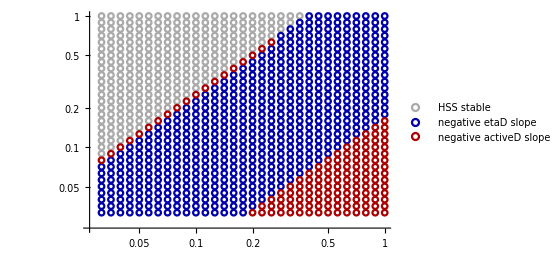

```mathematica
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopes,(#[[2,1]]>0)&&(#[[2,2]]>0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopes,(#[[2,1]]<0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSASlopes,(#[[2,1]]>0)&&(#[[2,2]]<0)&]
},{}],PlotMarkers->({Graphics[{#,Circle[]}],0.03}&/@{Lighter@Gray,Darker@Blue,(*Lighter@Blue,*)Darker@Red,Black}),PlotLegends->{"HSS stable","negative etaD slope","negative activeD slope"}]
```

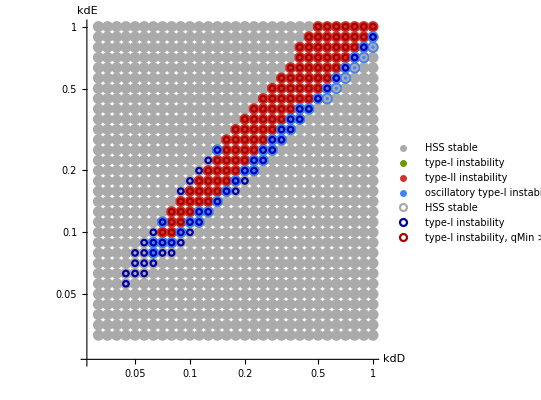

```mathematica
Show[
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==0&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==1&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==2&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==3&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==4&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==5&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==6&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]
},
{}],PlotStyle->({#,PointSize[0.02]}&/@Join[{Lighter@Gray},ColorData[90,"ColorList"]]),AxesLabel->(Style[#,FontSize->14]&/@{"kdD","kdE"}),
AspectRatio->1,TicksStyle->Directive[14],
AxesStyle->Thickness[0.002],PlotLegends->((
#[[1]]&/@DeleteCases[{#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==0&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==1&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==2&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==3&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==4&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==5&],
#[[2,1]]&/@Select[sweepLSA,#[[2,1]]==6&],
7&/@Select[sweepLSA,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]},{}])/.{0->"HSS stable",1->"type-III instability",2->"type-III + type-I instability with σ<0 in between",3->"type-I + type-III instability with σ>0 for q<qc",4->"type-I + type-III instability with σ<0 for q<qc",5->"type-I instability",6->"type-II instability",7->"oscillatory type-I instability"})],
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAPred,(#[[2,2,1]]==0&&#[[2,2,2]]==0&&#[[2,-2]]>0&&#[[2,-1]]<=0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAPred,(((#[[2,2,1]]>0)||(#[[2,2,2]]>0))&&#[[2,2,1]]<5&&#[[2,2,2]]<5&&#[[2,-2]]>0&&#[[2,-1]]<=0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAPred,(#[[2,-2]]<0&&#[[2,-1]]<=0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSAPred,(#[[2,-1]]>0)&]
},{}],PlotMarkers->({Graphics[{#,Circle[]}],0.03}&/@{Lighter@Gray,Darker@Blue,(*Lighter@Blue,*)Darker@Red,Black}),PlotLegends->{"HSS stable","type-I instability","type-I instability, qMin > 5","type-II instability","type-III instability"}]
]
```

```mathematica
10^-0.5
```

0.316228

#### kdE=10^-0.5

{0.316228,0.316228}

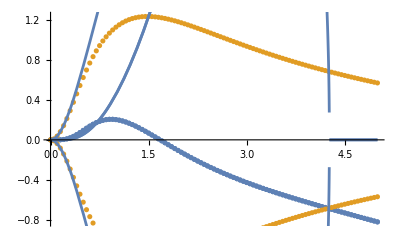

```mathematica
ps={10^-0.5,10^-0.5}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{0.354813,0.316228}

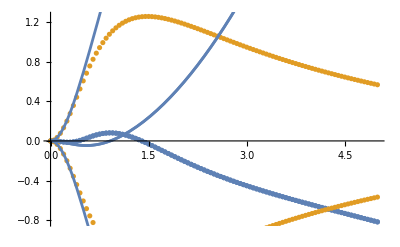

```mathematica
ps={10^-0.45,10^-0.5}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{0.398107,0.316228}

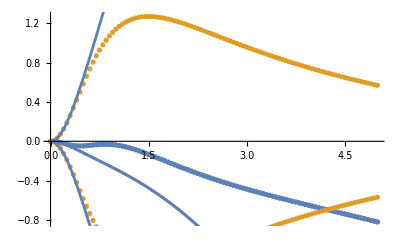

```mathematica
ps={10^-0.4,10^-0.5}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

#### kdE=10^-0.3

{0.398107,0.501187}

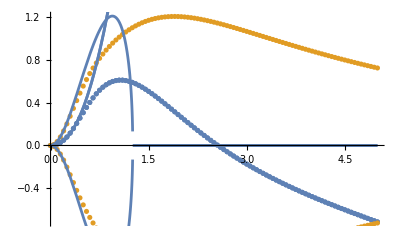

```mathematica
ps={10^-0.4,10^-0.3}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{0.501187,0.501187}

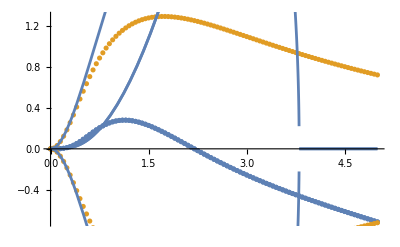

```mathematica
ps={10^-0.3,10^-0.3}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{0.630957,0.501187}

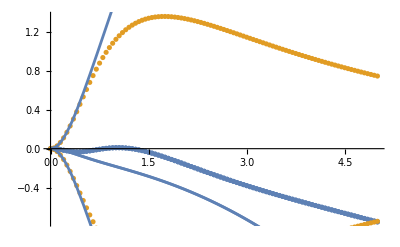

```mathematica
ps={10^-0.2,10^-0.3}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

#### kdD=10^-0.5

```mathematica
ps={10^-0.5,10^-0.5}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{0.316228,0.316228}

-Graphics-

{0.316228,0.281838}

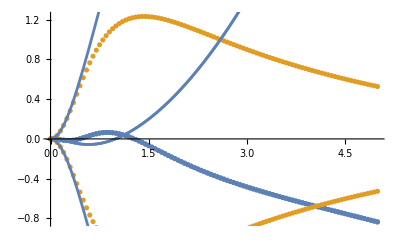

```mathematica
ps={10^-0.5,10^-0.55}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{0.316228,0.251189}

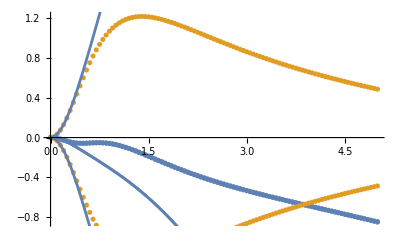

```mathematica
ps={10^-0.5,10^-0.6}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{0.316228,0.199526}

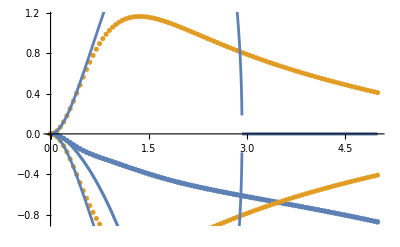

```mathematica
ps={10^-0.5,10^-0.7}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSAPred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

### Vary kdD, kdE, DE=0.1

```mathematica
Monitor[sweepLSA2=Table[
{
vps,
testInstab[Join[{kdD->vps[[1]],kdE->vps[[2]],DE->0.1},DeleteCases[paramsSkeletonScaled,(kdD->_)|(kdE->_)|(DE->_)]],"gpts"->100]
},{vps,Flatten[Outer[List,10^Range[-3,0,0.1],10^Range[-3,0,0.1]],1]}];,vps]
```

```mathematica
Monitor[sweepLSA2Pred=Table[
{
vps,
predDisp[Join[{kdD->vps[[1]],kdE->vps[[2]],DE->0.1},DeleteCases[paramsSkeletonScaled,(kdD->_)|(kdE->_)|(DE->_)]]]
},{vps,Flatten[Outer[List,10^Range[-3,0,0.1],10^Range[-3,0,0.1]],1]}];,vps]
```

```mathematica
Monitor[sweepLSA2Slopes=Table[
{
vps,
predSlopes[Join[{kdD->vps[[1]],kdE->vps[[2]]},DeleteCases[paramsSkeletonScaled,(kdD->_)|(kdE->_)]]]
},{vps,Flatten[Outer[List,10^Range[-3,0,0.1],10^Range[-3,0,0.1]],1]}];,vps]
```

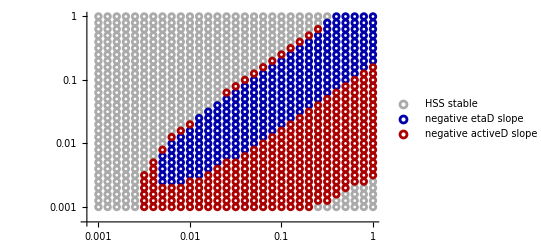

```mathematica
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Slopes,(#[[2,1]]>0)&&(#[[2,2]]>0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Slopes,(#[[2,1]]<0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Slopes,(#[[2,1]]>0)&&(#[[2,2]]<0)&]
},{}],PlotMarkers->({Graphics[{#,Circle[]}],0.03}&/@{Lighter@Gray,Darker@Blue,(*Lighter@Blue,*)Darker@Red,Black}),PlotLegends->{"HSS stable","negative etaD slope","negative activeD slope"}]
```

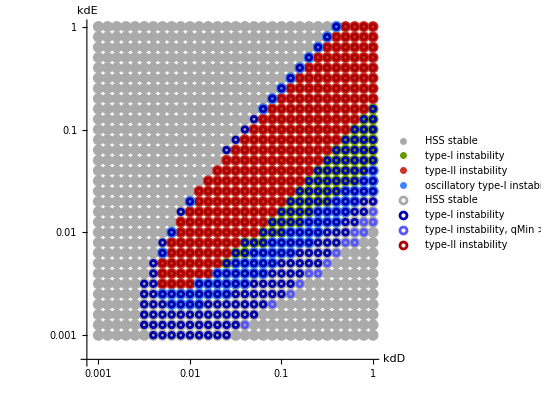

```mathematica
Show[
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==0&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==1&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==2&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==3&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==4&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==5&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==6&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]
},
{}],PlotStyle->({#,PointSize[0.02]}&/@Join[{Lighter@Gray},ColorData[90,"ColorList"]]),AxesLabel->(Style[#,FontSize->14]&/@{"kdD","kdE"}),
AspectRatio->1,TicksStyle->Directive[14],
AxesStyle->Thickness[0.002],PlotLegends->((
#[[1]]&/@DeleteCases[{#[[2,1]]&/@Select[sweepLSA2,#[[2,1]]==0&],
#[[2,1]]&/@Select[sweepLSA2,#[[2,1]]==1&],
#[[2,1]]&/@Select[sweepLSA2,#[[2,1]]==2&],
#[[2,1]]&/@Select[sweepLSA2,#[[2,1]]==3&],
#[[2,1]]&/@Select[sweepLSA2,#[[2,1]]==4&],
#[[2,1]]&/@Select[sweepLSA2,#[[2,1]]==5&],
#[[2,1]]&/@Select[sweepLSA2,#[[2,1]]==6&],
7&/@Select[sweepLSA2,#[[2,1]]==5&&Im@#[[2,-1]]!=0&]},{}])/.{0->"HSS stable",1->"type-III instability",2->"type-III + type-I instability with σ<0 in between",3->"type-I + type-III instability with σ>0 for q<qc",4->"type-I + type-III instability with σ<0 for q<qc",5->"type-I instability",6->"type-II instability",7->"oscillatory type-I instability"})],
ListLogLogPlot[DeleteCases[{
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Pred,(#[[2,2,1]]==0&&#[[2,2,2]]==0&&#[[2,-2]]>0&&#[[2,-1]]<=0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Pred,(((#[[2,2,1]]>0)||(#[[2,2,2]]>0))&&#[[2,2,1]]<5&&#[[2,2,2]]<5&&#[[2,-2]]>0&&#[[2,-1]]<=0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Pred,(((#[[2,2,1]]>5)||(#[[2,2,2]]>5))&&#[[2,-2]]>0&&#[[2,-1]]<=0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Pred,(#[[2,-2]]<0&&#[[2,-1]]<=0)&],
{#[[1,1]],#[[1,2]]}&/@Select[sweepLSA2Pred,(#[[2,-1]]>0)&]
},{}],PlotMarkers->({Graphics[{#,Circle[]}],0.03}&/@{Lighter@Gray,Darker@Blue,Lighter@Blue,Darker@Red,Black}),PlotLegends->{"HSS stable","type-I instability","type-I instability, qMin > 5","type-II instability","type-III instability"}]
]
```

#### kdD=1

{1,1/10}

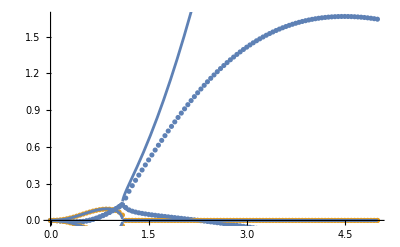

```mathematica
ps={10^0,10^-1}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{1,0.0398107}

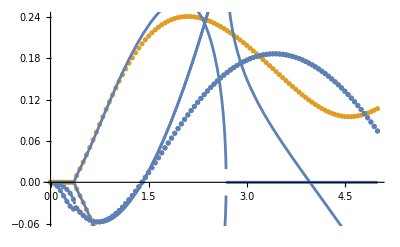

```mathematica
ps={10^0,10^-1.4}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{1,0.0251189}

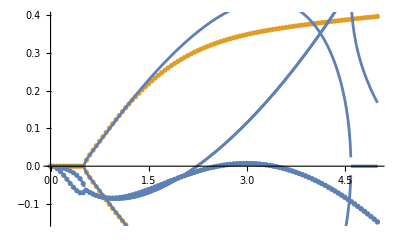

```mathematica
ps={10^0,10^-1.6}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{1,0.0158489}

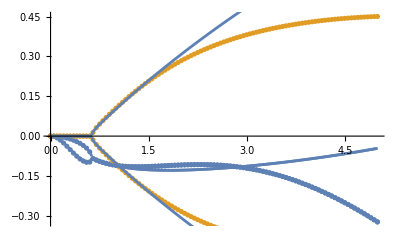

```mathematica
ps={10^0,10^-1.8}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{1,1/100}

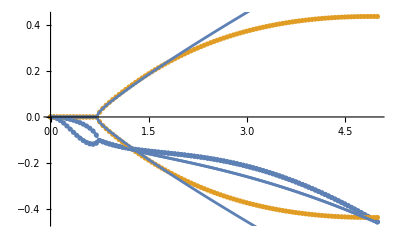

```mathematica
ps={10^0,10^-2}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

#### kdD=10^-1

{1/10,1/100}

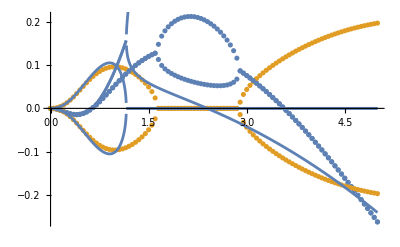

```mathematica
ps={10^-1,10^-2}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{1/10,0.00398107}

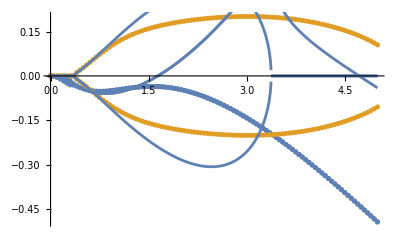

```mathematica
ps={10^-1,10^-2.4}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```

{1/10,0.00251189}

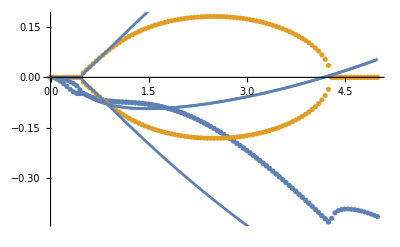

```mathematica
ps={10^-1,10^-2.6}
Show[
ListPlot[{{#[[1]],Re@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-1]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
ListPlot[{{#[[1]],Re@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]],
{#[[1]],Im@#[[2,-2]]}&/@Select[sweepLSA2,#[[1]]==ps&][[1,2,2]]}],
Plot[Re@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}],
Plot[Im@Select[sweepLSA2Pred,#[[1]]==ps&][[1,2,1]],{q,0,5}]
]
```